# A toy code for transforming math to circuits for analog computers

This is a printout from an explorative notebook of SvenK at 2019-12-04 to explore the feasibility of a “formula translator” for analog computers, without making use of anything else then a standard computer algebra system (namely Wolfram Mathematica 12). The code is written with the “Model-1” analog computer in mind (produced by analogparadigm.com)

## On Mathematica

Mathematica is a Computer Algebra System (CAS) based on LISP notation with a huge standard library. It also ships the most comprehensive ruleset for transforming challenging integrals, which is one the reasons for it’s market-dominance. However, I chose it for rapid prototyping only due to the beautiful access to the expression structure (aka the “abstract syntax tree” -- the symbol tree is the fundamental data structure) and it’s powerful pattern matching on that tree (Basically it’s an engine for tree manipulations).

Downside: Mathematica is proprietary and requires an expensive license (I use one from Frankfurt University).

```mathematica
(* A code sample: "example" is a variable holding an equation *)
example = a == b ⅇ^(-c x)+c/d
```

a==c/d+b ⅇ^(-c x)

```mathematica
(* Show the equation as LaTeX would render it *)
TraditionalForm[example]
```

a==b ⅇ^(-c x)+c/d

```mathematica
(* Show the actual S-expression-like representation; 
   roughly (car cdr) <-> car[cdr] *)
FullForm[example]
```

Equal[a,Plus[Times[c,Power[d,-1]],Times[b,Power[E,Times[-1,c,x]]]]]

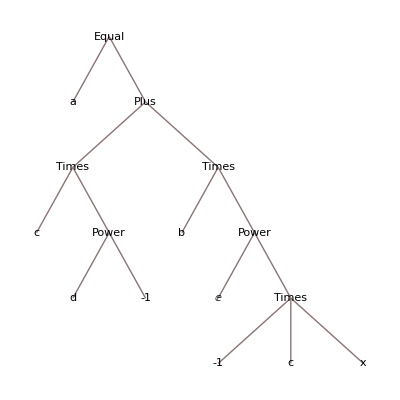

```mathematica
(* Visualize the tree of the S-expression *)
TreeForm[example]
```

The goal of the following section is to map the operations (Plus, Times, Power, ...) to primitive building blogs of the “Model 1” analog computer. Subsequently, each node and each edge gets a unique name which allows for serialization in terms of a simple “wiring plan”.

## Section 1) Transforming simple arithmetic expressions

```mathematica
AnalogParadigmParts= {
Adder,Multiplier,Integrator,  (* elementary parts *)
InputConstant,OutputVariable     (* helper parts *)
};
devName = Symbol[ToString@#<>"Dev"]&; (* map part -> device name *)
Terms2AnalogParadigm[expr_] := expr //.Dispatch@ {
Plus -> Adder,(* ∑ *)
Times -> Multiplier, (* ∏ *)
Integrate[x_,t]->Integrator[x] (* x must be formally x[t] else ∫ evaluates *)
}
```

In a real-life code, an suitable translation would already include a lot of tricks: Algebraic simplifications as well as knowledge about efficient (optimal) use of the analog computer components. However, in this toy code, we only examine very simple expressions.

The following are examples dealing with "special functions" not further used in the notepad. In general I pay no attention to implementation details on adders, etc.. We also neglect multiplicities/weights in this proof-of-concept.

Actually, the mathematica pattern matching system (together with reformulating terms) is quite powerful to allow this accessible approach to cover complex cases such as ...

```mathematica
EvenMoreTerms2AnalogParadigm = {
Plus[a_,Times[-1,b]]-> Substractor[a,b], (* a-b == a+(-b) in MMA *)
InverseFunction->Inverser,
Times[a_,Power[b_,-1]]-> Inverser[Multiplier[a,b]] ,(* a/b == a*(1/b) in MMA *)
Sqrt-> SquareRooter,
Power[1,t]->OneOverTime,
Power[x_,n_]-> IntegratePolynomials, (* ... *)
Abs->Abser, Min->LimitDown,Max->LimitUp, etc-> pp
};
```

The following allows for associating raw numbers to Potentiometers and variables to some kind of output device.

```mathematica
(* NB: This can only recognize equations of type x==f(x) *)
IO2AnalogParadigm[expr_]:=ReplaceAll[
Replace[expr, num_?NumericQ-> InputConstant[num]],
Equal[a_Symbol,b_]-> OutputVariable[a,b]];
Mathematica2AnalogParadigm = IO2AnalogParadigm@*Terms2AnalogParadigm;
```

Here is an example of how a super-simple expression with some constants (numbers) and input variables (a,b,c,d) transforms:

```mathematica
testEquation = f==a(b+c 5+d)+4a;
analogTestEq=Mathematica2AnalogParadigm[testEquation]
```

OutputVariable[f,Adder[Multiplier[4,a],Multiplier[a,Adder[b,Multiplier[5,c],d]]]]

#### Giving unique names to each Adder, Multiplier, ...

We now transform the tree structure of an expression in a way that each primitive operation (called “part”) is uniquly marked (which then allows to identify it with a physical “device”). For simplicity, the “devices” are just enumerated (they would be most likely given names when written out in a HDL by humans, or some “temporary variable” names when being used in a code generation as typically done for FORTRAN/C).

```mathematica
(* aexpr is the output of Mathematica2AnalogParadigm[some equation(s)] *)
exprParts[aexpr_] := Cases[indent@aexpr, Blank@#, Infinity]&/@AnalogParadigmParts;
exprDevsWithArgs[aexpr_]:=MapIndexed[Apply[devName[Head@#1][Last@#2],#1]&, exprParts@aexpr,{2}]
(* args still parts, not devs *)
exprPart2DevsWArgs[aexpr_] := Replace[Transpose@{Flatten@exprParts@aexpr,Flatten@exprDevsWithArgs@aexpr} ,
List->Rule,{2},Heads->True];
uniqueAnalogExpr[aexpr_]:=aexpr//.exprPart2DevsWArgs[aexpr];
```

The following table basically shows the mapping between “unnamed” or “anonymous” evaluation of operations (left column) and unique names of their physical manifestation. Compare also the subsequent tree of the unnamed AnalogParadigm primitives with the on with named ones:

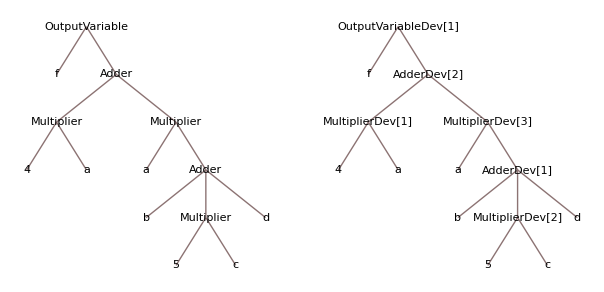

```mathematica
TableForm[ exprPart2DevsWArgs[analogTestEq]/.Rule->List,TableHeadings-> {None,{"Analog primtives","Physical devices"}}];
GraphicsGrid[{TreeForm@#@Mathematica2AnalogParadigm@testEquation&/@{Identity,uniqueAnalogExpr}}]
```

#### Identify the wiring

```mathematica
allSubtrees[aexpr_]:=Flatten[Cases[indent@uniqueAnalogExpr@aexpr,#[_][__],Infinity, Heads->True]&/@devName/@AnalogParadigmParts];
edgeList[n_]:=MapIndexed[{
If[LeafCount@#>1,(Head@#)[outJack],#],
(Head@n)[inJack[First@#2]] }&,List@@n];
wiring[aexpr_]:=Flatten[edgeList/@allSubtrees@aexpr, 1];
wiringWithoutJacks[aexpr_]:=wiring@aexpr//.{x_[inJack[_]]-> x,x_[outJack]-> x};
```

This code is not great but simple enough to demonstrate how to identify variables across the tree (which share a single value and therefore can/should be wired together). Interestingly, the tree is now no more a tree:

```mathematica
wiringWithoutJacks[analogTestEq]//TableForm;
wiring[analogTestEq]//TableForm
TreePlot[wiringWithoutJacks@analogTestEq/.{a_,b_}->(a->b),
Automatic, OutputVariableDev[1],(* optional line to define "root" element *) 
PlotTheme->"ClassicLabeled"]
```

b | AdderDev[1][inJack[1]]
MultiplierDev[2][outJack] | AdderDev[1][inJack[2]]
d | AdderDev[1][inJack[3]]
MultiplierDev[1][outJack] | AdderDev[2][inJack[1]]
MultiplierDev[3][outJack] | AdderDev[2][inJack[2]]
4 | MultiplierDev[1][inJack[1]]
a | MultiplierDev[1][inJack[2]]
5 | MultiplierDev[2][inJack[1]]
c | MultiplierDev[2][inJack[2]]
a | MultiplierDev[3][inJack[1]]
AdderDev[1][outJack] | MultiplierDev[3][inJack[2]]
f | OutputVariableDev[1][inJack[1]]
AdderDev[2][outJack] | OutputVariableDev[1][inJack[2]]

-Graphics-

#### Print a wiring list

```mathematica
AnalogParadigmCounter={ 
Adder-> 1./8., Multiplier-> 1./8., Integrator-> 1./4.,
Divider->1./2.,  InputConstant-> 1./8., OutputVariable-> 1./4.};
AnalogParadigmDev2Module = {
Adder -> "SUM8", Multiplier-> "MLT8", Integrator->"INT4",
 Divider-> "MSD2"(*missing mode*),InputConstant-> "PT8",
 OutputVariable-> "XIBNC" };
 (* beautifying: Write device addresses more compact/OOP-like *)
IObeautify[naming_]:=naming/.OutputVariableDev[n_][inout_]:> OutputVariableDev[n]; 
beautify[naming_]:=IObeautify@naming \
/.Map[#[n_]:> Symbol[ToString@#<>ToString@n]&,devName~Map~AnalogParadigmParts] \
/. {x_[outJack]:> ToString@x<>".output",x_[inJack[n_]]:> StringForm["``.input(``)",x,n]}
Equation2Wiring[analogEquations_,mmaEquations_:None]:=(
Print[Style["Wiring and component list", 18, Bold, Red]];
Print["To implement the expression:"];
Print["  ", TraditionalForm@If[mmaEquations~SameQ~None,analogEquations,mmaEquations]];
Print["Required Parts:"~Style~Bold];
Print["  Basic arithmetic units: ", StringForm@@({"`` x ``"}~Join~#)&/@  Transpose@{Length/@exprParts[analogEquations],AnalogParadigmParts}];
Print["  Model-1 modules: ",StringForm@@({"`` x ``"}~Join~#)&/@ ({Ceiling[Last@#*First@#/.AnalogParadigmCounter],First@#/.AnalogParadigmDev2Module}&/@Transpose@{AnalogParadigmParts,Length/@exprParts[analogEquations]})];
Print["Wiring:"~Style~Bold];
Scan[Print[StringForm["  `` -> ``", beautify@First@#, beautify@Last@#]]&,wiring[analogEquations]]
)
```

Here’s the written-out part and wiring plan for the test equation:

```mathematica
Equation2Wiring[analogTestEq,testEquation]
```

Wiring and component list

To implement the expression:

f==a (b+5 c+d)+4 a

Required Parts:

Basic arithmetic units: {2 x Adder,3 x Multiplier,0 x Integrator,0 x InputConstant,1 x OutputVariable}

Model-1 modules: {1 x SUM8,1 x MLT8,0 x INT4,0 x PT8,1 x XIBNC}

Wiring:

b -> AdderDev1.input(1)

MultiplierDev2.output -> AdderDev1.input(2)

d -> AdderDev1.input(3)

MultiplierDev1.output -> AdderDev2.input(1)

MultiplierDev3.output -> AdderDev2.input(2)

4 -> MultiplierDev1.input(1)

a -> MultiplierDev1.input(2)

5 -> MultiplierDev2.input(1)

c -> MultiplierDev2.input(2)

a -> MultiplierDev3.input(1)

AdderDev1.output -> MultiplierDev3.input(2)

f -> OutputVariableDev1

AdderDev2.output -> OutputVariableDev1

#### Review of the wiring

What a few lines of code can do:

Determine the material needed, tell about the input and output jacks to be connected.
Particular shortcomings:

It didn't enumerate Model-1 modules, i.e. did not take them into account at the wiring output.
General shortcomings:

The generated circuit is certainly not realistic. It is not optimized in terms of using only a minimal amount of hardware.

## Section 2) Transforming simple differential equations

```mathematica
lorentz={ 
D[x[t],t]==σ(y[t]-x[t]),
D[y[t],t]==x[t](ρ-z[t])-y[t],
D[z[t],t]==x [t]y[t] - β z[t]
};
params = { σ-> 10, β->2.6667,ρ->28};
lorentz//TableForm//TraditionalForm
```

x'(t)==σ (y(t)-x(t))
y'(t)==x(t) (ρ-z(t))-y(t)
z'(t)==x(t) y(t)-β z(t)

```mathematica
IntegrateEquation[x_==y_]:=Integrate[x,t]==Integrate[y,t]
integralLorentz=IntegrateEquation/@lorentz/.params//N;
integralLorentz//TableForm//TraditionalForm
```

x(t)==10. ∫(y(t)-x(t))ⅆt
y(t)==∫(x(t) (28-z(t))-y(t))ⅆt
z(t)==∫(x(t) y(t)-2.6667 z(t))ⅆt

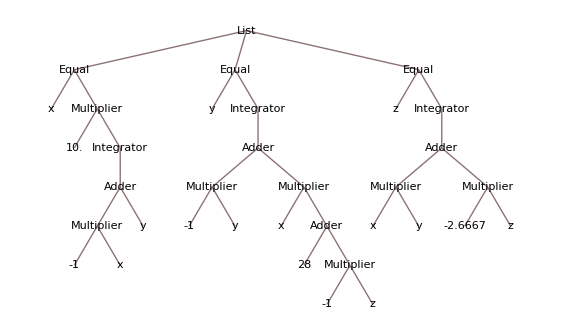

```mathematica
analogLorentz=Mathematica2AnalogParadigm[integralLorentz]/.{x[t]->x,y[t]->y,z[t]->z};  (* removing explicit time dependency *)
analogLorentz//TreeForm
```

#### Wiring the Lorentz attractor ODE (naively...)

```mathematica
Graph[wiringWithoutJacks[analogLorentz]/.{a_,b_}->(a->b), PlotTheme->"ClassicLabeled",GraphLayout->"GravityEmbedding"]
```

-Graphics-

It’s hard to tell something from these graphs, the layouting (and labeling) is not fine-tuned. The previous one shows the wiring (ignoring the jacks at the devices), while the next ones compares how the jack-aware connection graph looks like (i.e. the actual “isovoltage” lines, if you want).

```mathematica
GraphicsGrid[{{
Graph[wiringWithoutJacks[analogLorentz]/.{a_,b_}->(a->b), PlotTheme->"LargeGraph",GraphLayout->"SpringEmbedding"],
Graph[wiring[analogLorentz]/.{a_,b_}->(a->b), PlotTheme->"LargeGraph",GraphLayout->"SpringEmbedding"]
}},ImageSize->Large]
```

-Graphics-

```mathematica
Equation2Wiring[analogLorentz,TableForm@integralLorentz]
```

Wiring and component list

To implement the expression:

x(t)==10. ∫(y(t)-x(t))ⅆt
y(t)==∫(x(t) (28-z(t))-y(t))ⅆt
z(t)==∫(x(t) y(t)-2.6667 z(t))ⅆt

Required Parts:

Basic arithmetic units: {4 x Adder,7 x Multiplier,3 x Integrator,0 x InputConstant,0 x OutputVariable}

Model-1 modules: {1 x SUM8,1 x MLT8,1 x INT4,0 x PT8,0 x XIBNC}

Wiring:

MultiplierDev1.output -> AdderDev1.input(1)

y -> AdderDev1.input(2)

28 -> AdderDev2.input(1)

MultiplierDev4.output -> AdderDev2.input(2)

MultiplierDev3.output -> AdderDev3.input(1)

MultiplierDev5.output -> AdderDev3.input(2)

MultiplierDev6.output -> AdderDev4.input(1)

MultiplierDev7.output -> AdderDev4.input(2)

- continued -

-1 -> MultiplierDev1.input(1)

x -> MultiplierDev1.input(2)

10. -> MultiplierDev2.input(1)

IntegratorDev1.output -> MultiplierDev2.input(2)

-1 -> MultiplierDev3.input(1)

y -> MultiplierDev3.input(2)

-1 -> MultiplierDev4.input(1)

z -> MultiplierDev4.input(2)

x -> MultiplierDev5.input(1)

AdderDev2.output -> MultiplierDev5.input(2)

x -> MultiplierDev6.input(1)

y -> MultiplierDev6.input(2)

-2.6667 -> MultiplierDev7.input(1)

z -> MultiplierDev7.input(2)

AdderDev1.output -> IntegratorDev1.input(1)

AdderDev3.output -> IntegratorDev2.input(1)

AdderDev4.output -> IntegratorDev3.input(1)

#### Review of the Lorentz attractor wiring

The generated circuit differs a lot from the one proposed by Bernd in his books. An obvious reasons (telling from the equations itself) is that no efforts have been made to check any bounds (scaling of voltages/logic levels, probably introducing helper quantities). Furthermore, as said in the introductory example above, there is a number of general shortcomings, such as that we don’t enumerate Model-1 modules, i.e. don’t take them into account at the wiring output.